```mathematica
Subscript[Ψ, nlm][r_,θ_,φ_]=ⅇ^(-r/n) √(((2/n)^3 (-l+n-1)!)/(2 n (l+n)!)) ((2 r)/n)^l LaguerreL[-l+n-1,2 l+1,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]
```

2^(1+l) ⅇ^(-r/n) (r/n)^l √(((-1-l+n)!)/(n^4 (l+n)!)) LaguerreL[-1-l+n,1+2 l,(2 r)/n] SphericalHarmonicY[l,m,θ,φ]

```mathematica
Subscript[n, ex(28)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,3},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

1/78732 ⅇ^(-2 Re[r]) (629856+19683 ⅇ^Re[r] Abs[2-r]^2+13122 ⅇ^Re[r] Abs[r]^2+2304 ⅇ^((4 Re[r])/3) Abs[r]^2+64 ⅇ^((4 Re[r])/3) Abs[r]^4+128 ⅇ^((4 Re[r])/3) Abs[(-6+r) r]^2+32 ⅇ^((4 Re[r])/3) Abs[27-18 r+2 r^2]^2+6561 ⅇ^Re[r] r Conjugate[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Im[r]^2-768 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]^2)

```mathematica
Subscript[ñ, ex(28)][r_]=Subscript[n, ex(28)][r]*r^2
```

1/78732 ⅇ^(-2 Re[r]) r^2 (629856+19683 ⅇ^Re[r] Abs[2-r]^2+13122 ⅇ^Re[r] Abs[r]^2+2304 ⅇ^((4 Re[r])/3) Abs[r]^2+64 ⅇ^((4 Re[r])/3) Abs[r]^4+128 ⅇ^((4 Re[r])/3) Abs[(-6+r) r]^2+32 ⅇ^((4 Re[r])/3) Abs[27-18 r+2 r^2]^2+6561 ⅇ^Re[r] r Conjugate[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Im[r]^2-768 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]+64 ⅇ^((4 Re[r])/3) Abs[r]^2 Re[r]^2)

```mathematica
Subscript[n, TF(28)][r_]=((Sqrt[-0.0827625+2/r])^3)*HeavisideTheta[-0.0827625+2/r]/(3Pi^2)
```

```mathematica
Subscript[ñ, TF(28)][r_]=(4Pi r^2)Subscript[n, TF(28)][r]
```

```mathematica
Subscript[n, 3(2)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.48075)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.48075+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

```mathematica
Subscript[ñ, 3(2)][r_]=(4Pi r^2)Subscript[n, 3(2)][r]
```

```mathematica
4
```

```mathematica
Subscript[n, 3(10)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.164414+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

```mathematica
Subscript[ñ, 3(10)][r_]=(4Pi r^2)Subscript[n, 3(10)][r]
```

```mathematica
Subscript[n, 3(28)][r_]=∫_({a,θ}∈ImplicitRegion[(2/0.0827625)^2>r^2-2 r Cos[θ] a+a^2&&a≥0&&0≤θ≤π,{a,θ}]) (BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r Cos[θ])))] (-0.0827625+2/(√(a^2+r^2-2 a r Cos[θ])))^(3/2) Sin[θ])/(2 a π^2)
```

```mathematica
Subscript[ñ, 3(28)][r_]=(4Pi r^2)Subscript[n, 3(28)][r]
```

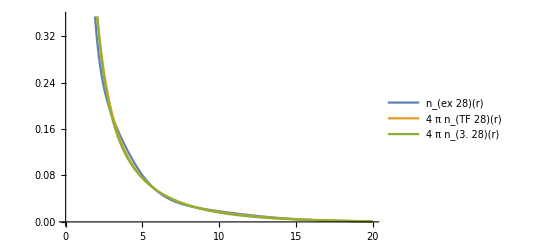

```mathematica
Plot[{Subscript[n, ex(28)][r],4Pi Subscript[n, TF(28)][r],4Pi Subscript[n, 3(28)][r]},{r,0,20},PlotLegends->"Expressions"]
```

```mathematica
Plot[{Subscript[n, ex(28)][r],4Pi Subscript[n, TF(28)][r],4Pi Subscript[n, 3(28)][r],Subscript[ñ, ex(28)][r],Subscript[ñ, TF(28)][r],Subscript[ñ, 3(28)][r]},{r,0,40},PlotLegends->"Expressions"]
```

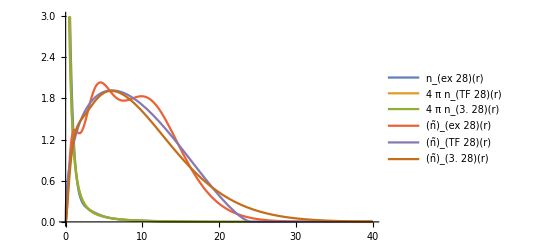

-Graphics-

```mathematica
Subscript[n, ex(2)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,1},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

8 ⅇ^(-2 Re[r])

```mathematica
Subscript[ñ, ex(2)][r_]=Subscript[n, ex(2)][r]*r^2
```

8 ⅇ^(-2 Re[r]) r^2

```mathematica
Subscript[n, ex(10)][r_]=Integrate[2*Sin[θ]Sum[Abs[Subscript[Ψ, nlm][r,θ,φ]]^2,{n,1,2},{l,0,n-1},{m,-l,l}],{θ,0,Pi},{φ,0,2Pi}]
```

-1/2 ⅇ^(-2 Re[r]) (-16-2 ⅇ^Re[r]-ⅇ^Re[r] Abs[r]^2+2 ⅇ^Re[r] Re[r])

```mathematica
Subscript[ñ, ex(10)][r_]=Subscript[n, ex(10)][r]*r^2
```

-1/2 ⅇ^(-2 Re[r]) r^2 (-16-2 ⅇ^Re[r]-ⅇ^Re[r] Abs[r]^2+2 ⅇ^Re[r] Re[r])

```mathematica
Subscript[n̂, TF(2)][r_]=((Sqrt[-0.48075+2/Max[r,0.25]])^3)*HeavisideTheta[-0.48075+2/Max[r,0.25]]/(3Pi^2)
```

(HeavisideTheta[-0.48075+2/Max[0.25,r]] (-0.48075+2/Max[0.25,r])^(3/2))/(3 π^2)

```mathematica
Subscript[n̄, TF(2)][r_]=(4Pi r^2)*Subscript[n̂, TF(2)][r]
```

(4 r^2 HeavisideTheta[-0.48075+2/Max[0.25,r]] (-0.48075+2/Max[0.25,r])^(3/2))/(3 π)

```mathematica
Subscript[n̂, TF(10)][r_]=((Sqrt[-0.164414+2/Max[r,0.25]])^3)*HeavisideTheta[-0.164414+2/Max[r,0.25]]/(3Pi^2)
```

(HeavisideTheta[-0.164414+2/Max[0.25,r]] (-0.164414+2/Max[0.25,r])^(3/2))/(3 π^2)

```mathematica
Subscript[n̄, TF(10)][r_]=(4Pi r^2)Subscript[n̂, TF(10)][r]
```

(4 r^2 HeavisideTheta[-0.164414+2/Max[0.25,r]] (-0.164414+2/Max[0.25,r])^(3/2))/(3 π)

```mathematica
Subscript[n̂, TF(28)][r_]=((Sqrt[-0.0827625+2/Max[r,0.25]])^3)*HeavisideTheta[-0.0827625+2/Max[r,0.25]]/(3Pi^2)
```

(HeavisideTheta[-0.0827625+2/Max[0.25,r]] (-0.0827625+2/Max[0.25,r])^(3/2))/(3 π^2)

```mathematica
Subscript[n̄, TF(28)][r_]=(4Pi r^2)Subscript[n̂, TF(28)][r]
```

(4 r^2 HeavisideTheta[-0.0827625+2/Max[0.25,r]] (-0.0827625+2/Max[0.25,r])^(3/2))/(3 π)

```mathematica
Subscript[n̂, 3(2)][r_]=∫_({a,t}∈ImplicitRegion[(2/0.48075)^2>r^2-2 r t a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (4Pi BesselJ[3,2 a √(-0.48075+2/Max[√(a^2+r^2-2 a r t),0.25])] (-0.48075+2/Max[√(a^2+r^2-2 a r t),0.25])^(3/2))/(2 a π^2)
```

```mathematica
Subscript[n̄, 3(2)][r_]=( r^2)*Subscript[n̂, 3(2)][r]
```

```mathematica
Subscript[n̂, 3(10)][r_]=∫_({a,t}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r t a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (4Pi BesselJ[3,2 a √(-0.164414+2/Max[√(a^2+r^2-2 a r t),0.25])] (-0.164414+2/Max[√(a^2+r^2-2 a r t),0.25])^(3/2))/(2 a π^2)
```

```mathematica
Subscript[n̄, 3(10)][r_]=( r^2)Subscript[n̂, 3(10)][r]
```

```mathematica
Subscript[n̂, 3(28)][r_]=∫_({a,t}∈ImplicitRegion[(2/0.0827625)^2>r^2-2 r t a+a^2&&a≥0&&-1≤t≤1,{a,t}]) (4Pi BesselJ[3,2 a √(-0.0827625+2/Max[√(a^2+r^2-2 a r t),0.25])] (-0.0827625+2/Max[√(a^2+r^2-2 a r t),0.25])^(3/2))/(2 a π^2)
```

```mathematica
Subscript[n̄, 3(28)][r_]=( r^2)Subscript[n̂, 3(28)][r]
```

```mathematica
Subscript[Overscript[n, #], 3(10)][r_]=∫_({a,t}∈ImplicitRegion[(2/0.164414)^2>r^2-2 r t a+a^2&&a≥0&&-1≤t≤1,{a,t}]) 1/(2 a π^2)4Pi BesselJ[3,2 a √(-0.164414+2/Max[√(a^2+r^2-2 a r t),0.0962121886/2])] (-0.164414+2/Max[√(a^2+r^2-2 a r t),0.0962121886/2])^(3/2)    (*to be continued*)
```

```mathematica
Subscript[A, 10]=Table[Subscript[Overscript[n, #], 3(10)][r],{r,0,10,0.0962121886}]                   (*to be continued*)
```

```mathematica
Solve[((Sqrt[-0.164414+2/(b/2)])^3)/(3Pi^2)==9,b]                  (*to be continued*)
```

{{b→0.0962122}}

```mathematica
Subscript[A, 2]=Table[Subscript[n̂, 3(2)][r],{r,0,6,b}]
```

```mathematica
Subscript[A, 28]=Table[Subscript[n̂, 3(28)][r],{r,0,15,b}]
```

```mathematica
Subscript[T, 2]=Table[Subscript[n̂, TF(2)][r],{r,0,6,b}]
```

```mathematica
Subscript[T, 10]=Table[Subscript[n̂, TF(10)][r],{r,0,10,0.0962121886}]
```

```mathematica
Subscript[T, 28]=Table[Subscript[n̂, TF(28)][r],{r,0,15,b}]
```

```mathematica
Subscript[Ā, 2]=Table[Subscript[n̄, 3(2)][r],{r,0,10,b}]
```

```mathematica
Subscript[Ā, 10]=Table[Subscript[n̄, 3(10)][r],{r,0,20,b}]
```

```mathematica
Subscript[Ā, 28]=Table[Subscript[n̄, 3(28)][r],{r,0,40,b}]
```

```mathematica
Subscript[T̄, 2]=Table[Subscript[n̄, TF(2)][r],{r,0,6,b}]
```

```mathematica
Subscript[T̄, 10]=Table[Subscript[n̄, TF(10)][r],{r,0,10,0.0962121886}]
```

```mathematica
Subscript[T̄, 28]=Table[Subscript[n̄, TF(28)][r],{r,0,15,b}]
```

```mathematica
Subscript[A, 2i]=Table[Subscript[n̂, 3(2)][r],{r,0,6,0.5}]
```

{1.93854,1.48197,0.6963,0.274172,0.136055,0.0684414,0.0370507,0.0209772,0.0116009,0.00704199,0.00386818,0.00244013,0.00134656}

```mathematica
Subscript[A, 10i]=Table[Subscript[n̂, 3(10)][r],{r,0,10,0.5}]
```

{2.69717,2.11366,1.10642,0.542571,0.324436,0.205545,0.141528,0.101331,0.0745659,0.0563138,0.0426386,0.0329509,0.0253147,0.0197599,0.0153307,0.0120078,0.00939069,0.0073528,0.00578756,0.0045222,0.00357501}

```mathematica
Subscript[A, 28i]=Table[Subscript[n̂, 3(28)][r],{r,0,15,0.5}]
```

{2.8902,2.27146,1.20483,0.60714,0.374145,0.248648,0.181999,0.13988,0.111402,0.0910515,0.0751277,0.0630334,0.0529852,0.0450884,0.0384045,0.0329858,0.0283886,0.0245403,0.0212849,0.0184806,0.0161133,0.0140326,0.0122715,0.0107102,0.00937679,0.00819703,0.0071754,0.00627991,0.00549223,0.00480971,0.00420164}

```mathematica
Subscript[T, 2i]=Table[4Pi Subscript[n̂, TF(2)][r],{r,0,6,0.5}]
```

{8.75086,2.80197,0.794754,0.334114,0.158801,0.0765571,0.0340225,0.011589,0.00113354,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Subscript[T, 10i]=Table[4Pi Subscript[n̂, TF(10)][r],{r,0,10,0.5}]
```

{9.30885,3.18813,1.05548,0.536371,0.324172,0.215055,0.151068,0.110206,0.0825077,0.0628922,0.0485303,0.0377395,0.0294651,0.0230176,0.0179301,0.0138772,0.0106266,0.00800895,0.00589893,0.00420256,0.0028491}

```mathematica
Subscript[T, 28i]=Table[4Pi Subscript[n̂, TF(28)][r],{r,0,15,0.5}]
```

{9.45474,3.29048,1.12669,0.593542,0.372831,0.2578,0.189366,0.14498,0.114384,0.0923165,0.0758343,0.0631765,0.0532335,0.0452751,0.0388042,0.0334716,0.0290261,0.025283,0.0221036,0.0193821,0.0170368,0.0150036,0.0132315,0.0116796,0.0103149,0.00911027,0.00804347,0.00709598,0.00625234,0.00549954,0.00482657}

```mathematica
Subscript[Ā, 2i]=Table[Subscript[n̄, 3(2)][r],{r,0,12,0.5}]
```

{0.,0.370493,0.6963,0.616887,0.54422,0.427759,0.333456,0.25697,0.185615,0.1426,0.0967046,0.0738139,0.0484763,0.0354079,0.0242334,0.0153955,0.0124098,0.00591985,0.00635134,0.00216047,0.00286494,0.00116172,0.000737981,0.00112896,-0.00037732}

```mathematica
Subscript[Ā, 10i]=Table[Subscript[n̄, 3(10)][r],{r,0,20,0.5}]
```

{0.,0.528415,1.10642,1.22078,1.29775,1.28466,1.27375,1.24131,1.19305,1.14035,1.06597,0.996766,0.911328,0.834856,0.751204,0.67544,0.601004,0.531239,0.468792,0.408129,0.357501,0.307416,0.267022,0.2277,0.195618,0.166202,0.140789,0.119679,0.0997789,0.0849998,0.0698613,0.0594608,0.0485168,0.0408904,0.0335393,0.0276138,0.0231069,0.0183481,0.0158131,0.0120844,0.0106542}

```mathematica
Subscript[Ā, 28i]=Table[Subscript[n̄, 3(28)][r],{r,0,30,0.5}]
```

{0.,0.567864,1.20483,1.36607,1.49658,1.55405,1.63799,1.71353,1.78243,1.84379,1.87819,1.90676,1.90747,1.90498,1.88182,1.85545,1.81687,1.77303,1.72407,1.66787,1.61133,1.5471,1.48486,1.41642,1.35026,1.28079,1.21264,1.14451,1.07648,1.01124,0.945368,0.883904,0.821974,0.764726,0.70804,0.655261,0.604523,0.556433,0.511766,0.468602,0.42967,0.391638,0.357844,0.325019,0.295713,0.267951,0.242579,0.219482,0.197653,0.178616,0.160086,0.144394,0.12898,0.115939,0.103432,0.0924777,0.082566,0.0733206,0.0655849,0.0578446,0.0517976}

```mathematica
Subscript[T̄, 2i]=Table[Subscript[n̄, TF(2)][r],{r,0,12,0.5}]
```

{0.,0.700493,0.794754,0.751756,0.635205,0.478482,0.306203,0.141965,0.0181366,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Subscript[T̄, 10i]=Table[Subscript[n̄, TF(10)][r],{r,0,20,0.5}]
```

{0.,0.797033,1.05548,1.20684,1.29669,1.3441,1.35961,1.35002,1.32012,1.27357,1.21326,1.14162,1.06074,0.972492,0.878573,0.780591,0.6801,0.578647,0.477813,0.379281,0.28491,0.196872,0.117911,0.0519642,0.00653427,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Subscript[T̄, 28i]=Table[Subscript[n̄, TF(28)][r],{r,0,30,0.5}]
```

{0.,0.822619,1.12669,1.33547,1.49132,1.61125,1.70429,1.776,1.83014,1.86941,1.89586,1.91109,1.9164,1.91287,1.9014,1.88278,1.85767,1.8267,1.79039,1.74923,1.70368,1.65415,1.60101,1.54463,1.48534,1.42348,1.35935,1.29324,1.22546,1.15628,1.08598,1.01484,0.94314,0.871154,0.799165,0.727463,0.656344,0.58612,0.517117,0.449685,0.384203,0.321087,0.260807,0.203908,0.151042,0.103029,0.0609804,0.0265967,0.00333407,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Subscript[EX, 2i]=Table[Subscript[n, ex(2)][r],{r,0,6,0.5}]
```

{8.,2.94304,1.08268,0.398297,0.146525,0.0539036,0.01983,0.00729506,0.0026837,0.000987278,0.000363199,0.000133614,0.0000491537}

```mathematica
Subscript[EX, 10i]=Table[Subscript[n, ex(10)][r],{r,0,10,0.5}]
```

{9.,3.32212,1.26662,0.537753,0.28186,0.187292,0.144298,0.116761,0.0942619,0.0745844,0.0576357,0.0435556,0.0322729,0.0235093,0.0168765,0.0119629,0.00838747,0.00582461,0.00401094,0.00274149,0.00186141}

```mathematica
Subscript[EX, 28i]=Table[Subscript[n, ex(28)][r],{r,0,15,0.5}]
```

{9.2963,3.43504,1.32359,0.58317,0.326537,0.230876,0.184397,0.151908,0.124339,0.1004,0.0803853,0.0644146,0.0521714,0.0430519,0.0363572,0.0314281,0.027714,0.0247945,0.0223721,0.0202513,0.0183147,0.0164994,0.0147785,0.0131459,0.0116066,0.0101691,0.00884201,0.00763122,0.00653942,0.00556588,0.00470688}

```mathematica
Subscript[OverTilde[EX], 2i]=Table[Subscript[ñ, ex(2)][r],{r,0,12,0.5}]
```

{0.,0.735759,1.08268,0.896167,0.5861,0.336897,0.17847,0.0893644,0.0429392,0.0199924,0.00907999,0.00404181,0.00176953,0.000763991,0.000325959,0.000137656,0.000057618,0.0000239288,9.86903×10^-6,4.04522×10^-6,1.64892×10^-6,6.68782×10^-7,2.70021×10^-7,1.08571×10^-7,4.34895×10^-8}

```mathematica
Subscript[OverTilde[EX], 10i]=Table[Subscript[ñ, ex(10)][r],{r,0,20,0.5}]
```

{0.,0.830529,1.26662,1.20994,1.12744,1.17057,1.29868,1.43032,1.50819,1.51033,1.44089,1.31756,1.16183,0.993269,0.826947,0.672913,0.536798,0.420828,0.324886,0.24742,0.186141,0.138513,0.102056,0.0745212,0.0539708,0.0387951,0.0276947,0.019645,0.0138533,0.00971583,0.00677956,0.00470832,0.00325542,0.00224154,0.00153743,0.00105064,0.000715504,0.000485688,0.000328674,0.000221772,0.000149228}

```mathematica
Subscript[OverTilde[EX], 28i]=Table[Subscript[ñ, ex(28)][r],{r,0,30,0.5}]
```

{0.,0.85876,1.32359,1.31213,1.30615,1.44298,1.65957,1.86087,1.98942,2.0331,2.00963,1.94854,1.87817,1.81894,1.7815,1.76783,1.77369,1.7914,1.81214,1.82768,1.83147,1.81906,1.7882,1.73855,1.67135,1.58893,1.4943,1.39079,1.28173,1.17023,1.05905,0.950512,0.846464,0.748293,0.656955,0.573029,0.496775,0.428189,0.367067,0.313055,0.265693,0.22446,0.188797,0.158144,0.131945,0.109674,0.0908373,0.0749795,0.061689,0.0505968,0.0413759,0.0337393,0.0274373,0.0222541,0.0180049,0.0145319,0.0117017,0.00940178,0.00753769,0.00603073,0.00481544}

```mathematica
{Subscript[n, 3(2)][0.25],Table[Subscript[n, 3(2)][r],{r,0.5,6,0.5}]}
```

{0.292573,{0.148916,0.0526275,0.0224151,0.0106715,0.00547689,0.00295678,0.00165061,0.000941873,0.000545227,0.00031863,0.000187396,0.00011068}}

```mathematica
Subscript[A^o, 3(2)]=4Pi{0.2925729614960424,0.14891599673776357,0.05262745303755851,0.022415072082854134,0.010671520492974177,0.005476887503273732,0.002956784531535389,0.0016506127489984844,0.0009418733273501741,0.0005452274047894096,0.00031862954433504114,0.000187396281427873,0.00011068026704277414}
```

{3.67658,1.87133,0.661336,0.281676,0.134102,0.0688246,0.0371561,0.0207422,0.0118359,0.00685153,0.00400402,0.00235489,0.00139085}

```mathematica
{Subscript[n, 3(10)][0.25],Table[Subscript[n, 3(10)][r],{r,0.5,10,0.5}]}
```

{0.354656,{0.199643,0.0851285,0.0438497,0.0256129,0.0164205,0.0112489,0.00805872,0.00594471,0.00446962,0.00340334,0.00261405,0.00202032,0.00156862,0.00122213,0.000954683,0.000747245,0.000585742,0.000459622,0.000360905,0.000283501}}

```mathematica
Subscript[A^o, 3(10)]=4Pi{0.35465630191945685,0.1996427381364232,0.08512845890812877,0.04384965335767788,0.025612882129609663,0.01642051948389115,0.011248864166518161,0.008058718546761257,0.005944714344591921,0.004469622155808062,0.003403338038649454,0.0026140547229831384,0.002020323323019198,0.0015686199464934522,0.0012221295299595202,0.0009546827068470629,0.0007472446407302814,0.0005857416069409679,0.00045962160196934927,0.00036090521960068753,0.00028350123285006575}
```

{4.45674,2.50878,1.06976,0.551031,0.321861,0.206346,0.141357,0.101269,0.0747035,0.0561669,0.0427676,0.0328492,0.0253881,0.0197119,0.0153577,0.0119969,0.00939015,0.00736065,0.00577578,0.00453527,0.00356258}

```mathematica
{Subscript[n, 3(28)][0.25],Table[Subscript[n, 3(28)][r],{r,0.5,15,0.5}]}
```

{0.370409,{0.21231,0.0929291,0.0490054,0.0295568,0.0198587,0.0144638,0.0111302,0.00887352,0.00723544,0.00598803,0.0050081,0.00422249,0.00358376,0.00305883,0.0026235,0.00225956,0.00195305,0.00169317,0.00147148,0.00128135,0.00111753,0.00097582,0.000852836,0.000745816,0.000652488,0.000570963,0.000499656,0.000437226,0.000382529,0.000334587}}

```mathematica
Subscript[A^o, 3(28)]=4Pi{0.3704092537971699,0.212309644412523,0.09292907726570462,0.0490053722334228,0.029556837237001417,0.019858730089751114,0.014463761076942283,0.01113023461127294,0.008873518286450487,0.00723543529407982,0.005988032826650052,0.005008097472412625,0.004222494256682422,0.0035837623202735953,0.0030588260580928723,0.0026234986710087314,0.0022595592088607624,0.00195305320000661,0.0016931709920985512,0.001471479777158141,0.0012813495371653601,0.0011175280608772087,0.0009758198907694551,0.0008528364123196396,0.0007458161295436746,0.0006524883857926795,0.0005709631747350761,0.0004996561154182111,0.0004372255668709445,0.00038252910521773816,0.000334587022772065}
```

{4.6547,2.66796,1.16778,0.61582,0.371422,0.249552,0.181757,0.139867,0.111508,0.0909232,0.0752478,0.0629336,0.0530614,0.0450349,0.0384383,0.0329679,0.0283945,0.0245428,0.021277,0.0184912,0.0161019,0.0140433,0.0122625,0.0107171,0.0093722,0.00819941,0.00717493,0.00627886,0.00549434,0.004807,0.00420454}

```mathematica
Subscript[(Ā)^o, 3(2)]=Table[Subscript[ñ, 3(2)][r],{r,0,12,0.5}]
```

{0.,0.467833,0.661336,0.633771,0.536409,0.430154,0.334404,0.254092,0.189375,0.138743,0.1001,0.0712355,0.0500706,0.0348077,0.0239569,0.0163403,0.0110533,0.00742098,0.00494742,0.00327704,0.00215719,0.0014126,0.000919916,0.000596056,0.000384538}

```mathematica
Subscript[(Ā)^o, 3(10)]=Table[Subscript[ñ, 3(10)][r],{r,0,20,0.5}]
```

{0.,0.627196,1.06976,1.23982,1.28744,1.28966,1.27222,1.24054,1.19526,1.13738,1.06919,0.993688,0.913973,0.832826,0.752529,0.674825,0.60097,0.531807,0.467838,0.409308,0.356258,0.308579,0.266055,0.22839,0.195246,0.166252,0.141031,0.119204,0.10041,0.0842991,0.070549,0.0588627,0.0489684,0.040623,0.0335732,0.027733,0.0228272,0.0187433,0.0153547,0.0125496,0.0102348}

```mathematica
Subscript[(Ā)^o, 3(28)]=Table[Subscript[ñ, 3(28)][r],{r,0,30,0.5}]
```

{0.,0.66699,1.16778,1.38559,1.48569,1.5597,1.63581,1.71337,1.78413,1.84119,1.8812,1.90374,1.91021,1.90272,1.88348,1.85444,1.81725,1.77322,1.72344,1.66883,1.61019,1.54827,1.48376,1.41733,1.3496,1.28116,1.21256,1.14432,1.07689,1.01067,0.946023,0.883241,0.822578,0.764237,0.708374,0.655103,0.604502,0.556617,0.511453,0.469004,0.429227,0.392072,0.357463,0.325313,0.295531,0.26801,0.242639,0.219311,0.197901,0.178311,0.160409,0.144087,0.129238,0.115754,0.10353,0.0924719,0.0824837,0.073478,0.065372,0.0580871,0.0515513}

```mathematica
Subscript[d^0, 3(2)]=Abs[Subscript[A^o, 3(2)]-Subscript[EX, 2i]]
```

{4.32342,1.0717,0.421346,0.11662,0.0124228,0.014921,0.017326,0.0134472,0.00915223,0.00586425,0.00364082,0.00222128,0.0013417}

```mathematica
Subscript[d^0, 3(10)]=Abs[Subscript[A^o, 3(10)]-Subscript[EX, 10i]]
```

{4.54326,0.813333,0.196866,0.0132781,0.0400006,0.0190546,0.00294029,0.0154917,0.0195584,0.0184175,0.0148681,0.0107064,0.0068848,0.00379746,0.00151874,0.000034,0.00100269,0.00153603,0.00176483,0.00179378,0.00170117}

```mathematica
Subscript[d^0, 3(28)]=Abs[Subscript[A^o, 3(28)]-Subscript[EX, 28i]]
```

{4.6416,0.767079,0.155809,0.0326496,0.0448857,0.018676,0.00264005,0.0120409,0.0128306,0.00947674,0.00513749,0.00148104,0.000890024,0.00198299,0.00208112,0.00153978,0.000680475,0.000251717,0.00109505,0.00176015,0.00221277,0.00245615,0.00251597,0.00242888,0.00223438,0.00196971,0.00166707,0.00135236,0.00104508,0.000758881,0.00050234}

```mathematica
Subscript[(d̄)^0, 3(2)]=Abs[Subscript[(Ā)^o, 3(2)]-Subscript[OverTilde[EX], 2i]]
```

{0.,0.267925,0.421346,0.262396,0.0496913,0.0932564,0.155934,0.164728,0.146436,0.118751,0.0910204,0.0671936,0.048301,0.0340438,0.023631,0.0162027,0.0109957,0.00739705,0.00493755,0.003273,0.00215554,0.00141193,0.000919646,0.000595948,0.000384495}

```mathematica
Subscript[(d̄)^0, 3(10)]=Abs[Subscript[(Ā)^o, 3(10)]-Subscript[OverTilde[EX], 10i]]
```

{0.,0.203333,0.196866,0.0298756,0.160002,0.119091,0.0264626,0.189774,0.312935,0.372953,0.371704,0.323868,0.247853,0.160443,0.0744181,0.0019125,0.064172,0.110978,0.142952,0.161888,0.170117,0.170066,0.163999,0.153869,0.141275,0.127457,0.113336,0.0995585,0.0865563,0.0745833,0.0637694,0.0541543,0.0457129,0.0383815,0.0320358,0.0266823,0.0221117,0.0182576,0.015026,0.0123278,0.0100856}

```mathematica
Subscript[(d̄)^0, 3(28)]=Abs[Subscript[(Ā)^o, 3(28)]-Subscript[OverTilde[EX], 28i]]
```

{0.,0.19177,0.155809,0.0734615,0.179543,0.116725,0.0237604,0.147501,0.20529,0.191904,0.128437,0.0448013,0.0320409,0.0837814,0.101975,0.0866126,0.0435504,0.0181866,0.0886993,0.158854,0.221277,0.27079,0.304432,0.321219,0.321751,0.307768,0.281735,0.246467,0.204836,0.159555,0.113027,0.0672707,0.0238862,0.0159445,0.0514198,0.0820744,0.107728,0.128428,0.144385,0.155949,0.163534,0.167612,0.168665,0.16717,0.163586,0.158335,0.151802,0.144332,0.136212,0.127714,0.119033,0.110348,0.101801,0.0934999,0.0855255,0.07794,0.070782,0.0640762,0.0578344,0.0520564,0.0467359}

```mathematica
Subscript[d, 3(2)]=Abs[Subscript[EX, 2i]-Subscript[A, 2i]]
```

{6.06146,1.46107,0.386382,0.124125,0.0104702,0.0145378,0.0172207,0.0136821,0.00891721,0.00605471,0.00350498,0.00230651,0.00129741}

```mathematica
Subscript[d, 3(10)]=Abs[Subscript[EX, 10i]-Subscript[A, 10i]]
```

{6.30283,1.20846,0.160202,0.00481806,0.0425761,0.0182536,0.00277003,0.0154294,0.019696,0.0182706,0.0149971,0.0106046,0.00695828,0.00374942,0.00154578,0.0000449267,0.00100322,0.00152818,0.00177662,0.00178071,0.0017136}

```mathematica
Subscript[d, 3(28)]=Abs[Subscript[EX, 28i]-Subscript[A, 28i]]
```

{6.4061,1.16358,0.118757,0.0239699,0.047608,0.017772,0.00239779,0.0120276,0.0129366,0.00934844,0.00525764,0.00138126,0.000813843,0.0020365,0.00204728,0.00155771,0.000674581,0.000254252,0.00108721,0.00177075,0.00220142,0.0024668,0.00250694,0.00243578,0.0022298,0.0019721,0.0016666,0.00135131,0.00104719,0.000756171,0.000505247}

```mathematica
Subscript[d̄, 3(2)]=Abs[Subscript[OverTilde[EX], 2i]-Subscript[Ā, 2i]]
```

{0.,0.365266,0.386382,0.27928,0.0418808,0.0908614,0.154986,0.167606,0.142675,0.122608,0.0876246,0.0697721,0.0467068,0.0346439,0.0239074,0.0152579,0.0123521,0.00589592,0.00634147,0.00215642,0.00286329,0.00116105,0.000737711,0.00112885,0.000377364}

```mathematica
Subscript[d̄, 3(10)]=Abs[Subscript[OverTilde[EX], 10i]-Subscript[Ā, 10i]]
```

{0.,0.302114,0.160202,0.0108406,0.170304,0.114085,0.0249303,0.18901,0.315136,0.36998,0.374928,0.32079,0.250498,0.158413,0.075743,0.00252713,0.064206,0.110411,0.143906,0.160709,0.17136,0.168902,0.164966,0.153178,0.141647,0.127407,0.113095,0.100034,0.0859256,0.075284,0.0630818,0.0547525,0.0452613,0.0386488,0.0320018,0.0265632,0.0223914,0.0178624,0.0154844,0.0118626,0.010505}

```mathematica
Subscript[d̄, 3(28)]=Abs[Subscript[OverTilde[EX], 28i]-Subscript[Ā, 28i]]
```

{0.,0.290896,0.118757,0.0539323,0.190432,0.111075,0.0215801,0.147338,0.206985,0.189306,0.131441,0.041783,0.0292984,0.0860423,0.100317,0.0876215,0.0431732,0.0183697,0.0880637,0.15981,0.220142,0.271965,0.303339,0.322131,0.321091,0.30814,0.281656,0.246276,0.205249,0.158985,0.113681,0.0666075,0.0244903,0.0164337,0.0510852,0.0822315,0.107749,0.128244,0.144698,0.155547,0.163976,0.167178,0.169047,0.166876,0.163768,0.158276,0.151741,0.144503,0.135964,0.128019,0.11871,0.110654,0.101543,0.0936852,0.0854267,0.0779458,0.0708643,0.0639188,0.0580472,0.0518139,0.0469821}

```mathematica
Subscript[d, TF(2)]=Abs[Subscript[EX, 2i]-Subscript[T, 2i]]
```

{0.750858,0.141062,0.287928,0.064183,0.012276,0.0226535,0.0141925,0.00429394,0.00155017,0.000987278,0.000363199,0.000133614,0.0000491537}

```mathematica
Subscript[d, TF(10)]=Abs[Subscript[EX, 10i]-Subscript[T, 10i]]
```

{0.308851,0.133984,0.21114,0.00138142,0.0423117,0.0277637,0.00677023,0.00655494,0.0117542,0.0116922,0.00910544,0.00581607,0.00280783,0.000491747,0.00105359,0.00191427,0.0022391,0.00218434,0.00188799,0.00146107,0.000987686}

```mathematica
Subscript[d, TF(28)]=Abs[Subscript[EX, 28i]-Subscript[T, 28i]]
```

{0.158439,0.144565,0.196904,0.0103717,0.0462941,0.0269241,0.00496863,0.00692787,0.00995493,0.00808344,0.00455104,0.0012381,0.00106205,0.0022232,0.00244693,0.0020435,0.00131216,0.000488497,0.000268516,0.00086922,0.00127786,0.00149583,0.00154702,0.00146634,0.0012917,0.00105886,0.000798536,0.000535237,0.000287083,0.0000663476,0.00011969}

```mathematica
Subscript[d̄, TF(2)]=Abs[Subscript[OverTilde[EX], 2i]-Subscript[T̄, 2i]]
```

{0.,0.0352655,0.287928,0.144412,0.0491041,0.141584,0.127732,0.0526008,0.0248027,0.0199924,0.00907999,0.00404181,0.00176953,0.000763991,0.000325959,0.000137656,0.000057618,0.0000239288,9.86903×10^-6,4.04522×10^-6,1.64892×10^-6,6.68782×10^-7,2.70021×10^-7,1.08571×10^-7,4.34895×10^-8}

```mathematica
Subscript[d̄, TF(10)]=Abs[Subscript[OverTilde[EX], 10i]-Subscript[T̄, 10i]]
```

{0.,0.033496,0.21114,0.00310819,0.169247,0.173523,0.0609321,0.080298,0.188067,0.236767,0.227636,0.175936,0.101082,0.0207763,0.0516257,0.107678,0.143302,0.157818,0.152927,0.131862,0.0987686,0.0583586,0.0158551,0.022557,0.0474365,0.0387951,0.0276947,0.019645,0.0138533,0.00971583,0.00677956,0.00470832,0.00325542,0.00224154,0.00153743,0.00105064,0.000715504,0.000485688,0.000328674,0.000221772,0.000149228}

```mathematica
Subscript[d̄, TF(28)]=Abs[Subscript[OverTilde[EX], 28i]-Subscript[T̄, 28i]]
```

{0.,0.0361413,0.196904,0.0233363,0.185176,0.168276,0.0447177,0.0848664,0.159279,0.16369,0.113776,0.0374526,0.0382338,0.0939303,0.119899,0.114947,0.0839784,0.0352939,0.0217498,0.0784471,0.127786,0.164915,0.187189,0.193924,0.186005,0.165446,0.134953,0.0975469,0.0562683,0.0139496,0.0269303,0.0643294,0.0966757,0.122861,0.142211,0.154434,0.159569,0.157931,0.15005,0.13663,0.118509,0.096627,0.0720096,0.0457647,0.019097,0.00664505,0.0298568,0.0483828,0.058355,0.0505968,0.0413759,0.0337393,0.0274373,0.0222541,0.0180049,0.0145319,0.0117017,0.00940178,0.00753769,0.00603073,0.00481544}

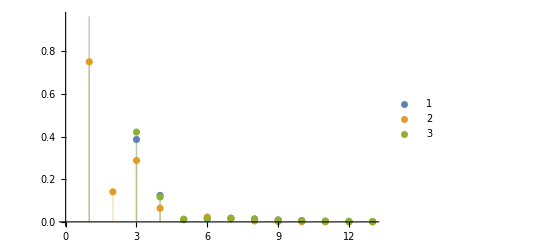

```mathematica
ListPlot[{Subscript[d, 3(2)],Subscript[d, TF(2)],Subscript[d^0, 3(2)]},Filling->Axis,PlotLegends->Automatic]
```

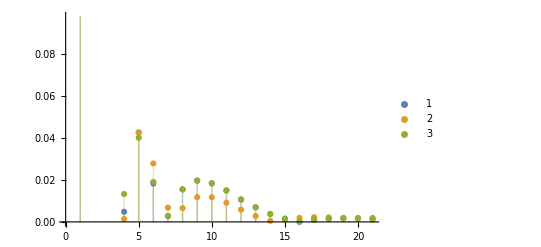

```mathematica
ListPlot[{Subscript[d, 3(10)],Subscript[d, TF(10)],Subscript[d^0, 3(10)]},Filling->Axis,PlotLegends->Automatic]
```

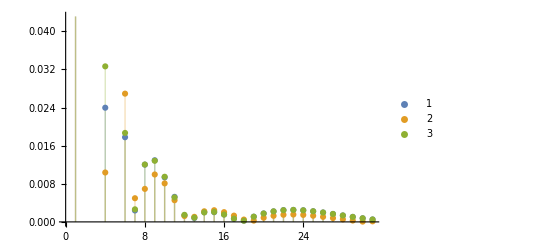

```mathematica
ListPlot[{Subscript[d, 3(28)],Subscript[d, TF(28)],Subscript[d^0, 3(28)]},Filling->Axis,PlotLegends->Automatic]
```

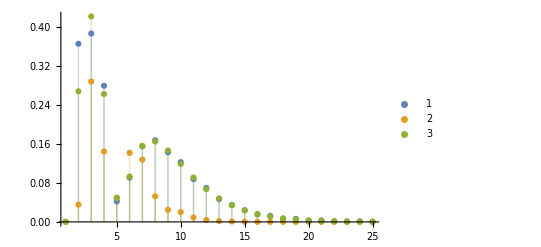

```mathematica
ListPlot[{Subscript[d̄, 3(2)],Subscript[d̄, TF(2)],Subscript[(d̄)^0, 3(2)]},Filling->Axis,PlotLegends->Automatic,PlotRange->All]
```

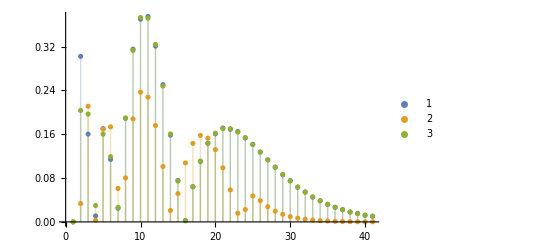

```mathematica
ListPlot[{Subscript[d̄, 3(10)],Subscript[d̄, TF(10)],Subscript[(d̄)^0, 3(10)]},Filling->Axis,PlotLegends->Automatic]
```

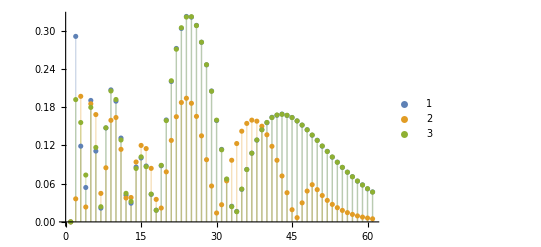

```mathematica
ListPlot[{Subscript[d̄, 3(28)],Subscript[d̄, TF(28)],Subscript[(d̄)^0, 3(28)]},Filling->Axis,PlotLegends->Automatic]
```

```mathematica
Mean[Subscript[d, 3(2)]]-Mean[Subscript[d, TF(2)]]
```

0.523884

```mathematica
Mean[Subscript[d, 3(10)]]-Mean[Subscript[d, TF(10)]]
```

0.335564

```mathematica
Mean[Subscript[d, 3(28)]]-Mean[Subscript[d, TF(28)]]
```

0.232601

```mathematica
Mean[Subscript[d̄, 3(2)]]-Mean[Subscript[d̄, TF(2)]]
```

0.0465134

```mathematica
Mean[Subscript[d̄, 3(10)]]-Mean[Subscript[d̄, TF(10)]]
```

0.0526238

```mathematica
Mean[Subscript[d̄, 3(28)]]-Mean[Subscript[d̄, TF(28)]]
```

0.0490579

```mathematica
Mean[Subscript[d, 3(2)]]-Mean[Subscript[d^0, 3(2)]]
Mean[Subscript[d, 3(10)]]-Mean[Subscript[d^0, 3(10)]]
Mean[Subscript[d, 3(28)]]-Mean[Subscript[d^0, 3(28)]]
Mean[Subscript[d̄, 3(2)]]-Mean[Subscript[(d̄)^0, 3(2)]]
Mean[Subscript[d̄, 3(10)]]-Mean[Subscript[(d̄)^0, 3(10)]]
Mean[Subscript[d̄, 3(28)]]-Mean[Subscript[(d̄)^0, 3(28)]]
```

0.544208

0.100533

0.121583

0.00278182

-0.151803

0.000715803

```mathematica
Mean[Subscript[d, TF(2)]]-Mean[Subscript[d^0, 3(2)]]
Mean[Subscript[d, TF(10)]]-Mean[Subscript[d^0, 3(10)]]
Mean[Subscript[d, TF(28)]]-Mean[Subscript[d^0, 3(28)]]
Mean[Subscript[d̄, TF(2)]]-Mean[Subscript[(d̄)^0, 3(2)]]
Mean[Subscript[d̄, TF(10)]]-Mean[Subscript[(d̄)^0, 3(10)]]
Mean[Subscript[d̄, TF(28)]]-Mean[Subscript[(d̄)^0, 3(28)]]
```

0.0203237

-0.235031

-0.111018

-0.0437315

-0.204426

-0.048342

```mathematica
TrimmedMean[Subscript[d, 3(2)]]-TrimmedMean[Subscript[d, TF(2)]]
```

0.523884

```mathematica
TrimmedMean[Subscript[d, 3(10)]]-TrimmedMean[Subscript[d, TF(10)]]
```

0.0554379

```mathematica
TrimmedMean[Subscript[d, 3(28)]]-TrimmedMean[Subscript[d, TF(28)]]
```

0.0345261

```mathematica
TrimmedMean[Subscript[d̄, 3(2)]]-TrimmedMean[Subscript[d̄, TF(2)]]
```

0.0462774

```mathematica
TrimmedMean[Subscript[d̄, 3(10)]]-TrimmedMean[Subscript[d̄, TF(10)]]
```

0.0506673

```mathematica
TrimmedMean[Subscript[d̄, 3(28)]]-TrimmedMean[Subscript[d̄, TF(28)]]
```

```mathematica
TrimmedMean[Subscript[d, 3(2)]]-TrimmedMean[Subscript[d^0, 3(2)]]
TrimmedMean[Subscript[d, 3(10)]]-TrimmedMean[Subscript[d^0, 3(10)]]
TrimmedMean[Subscript[d, 3(28)]]-TrimmedMean[Subscript[d^0, 3(28)]]
TrimmedMean[Subscript[d̄, 3(2)]]-TrimmedMean[Subscript[(d̄)^0, 3(2)]]
TrimmedMean[Subscript[d̄, 3(10)]]-TrimmedMean[Subscript[(d̄)^0, 3(10)]]
TrimmedMean[Subscript[d̄, 3(28)]]-TrimmedMean[Subscript[(d̄)^0, 3(28)]]
```

0.555595

0.018506

-0.0783169

0.00454388

0.0514818

0.000770318

```mathematica
TrimmedMean[Subscript[d, TF(2)]]-TrimmedMean[Subscript[d^0, 3(2)]]
TrimmedMean[Subscript[d, TF(10)]]-TrimmedMean[Subscript[d^0, 3(10)]]
TrimmedMean[Subscript[d, TF(28)]]-TrimmedMean[Subscript[d^0, 3(28)]]
TrimmedMean[Subscript[d̄, TF(2)]]-TrimmedMean[Subscript[(d̄)^0, 3(2)]]
TrimmedMean[Subscript[d̄, TF(10)]]-TrimmedMean[Subscript[(d̄)^0, 3(10)]]
TrimmedMean[Subscript[d̄, TF(28)]]-TrimmedMean[Subscript[(d̄)^0, 3(28)]]
```

0.0317112

-0.0871369

-0.0223783

-0.0417335

-0.0493906

0.0440492

```mathematica
Subscript[P, 3(2)]=Subscript[d, 3(2)]/Subscript[EX, 2i]
Subscript[P, 3(10)]=Subscript[d, 3(10)]/Subscript[EX, 10i]
Subscript[P, 3(28)]=Subscript[d, 3(28)]/Subscript[EX, 28i]
Subscript[P̄, 3(2)]=Subscript[d̄, 3(2)]/Subscript[OverTilde[EX], 2i]
Subscript[P̄, 3(10)]=Subscript[d̄, 3(10)]/Subscript[OverTilde[EX], 10i]
Subscript[P̄, 3(28)]=Subscript[d̄, 3(28)]/Subscript[OverTilde[EX], 28i]


Subscript[P, TF(2)]=Subscript[d, TF(2)]/Subscript[EX, 2i]
Subscript[P, TF(10)]=Subscript[d, TF(10)]/Subscript[EX, 10i]
Subscript[P, TF(28)]=Subscript[d, TF(28)]/Subscript[EX, 28i]
Subscript[P̄, TF(2)]=Subscript[d̄, TF(2)]/Subscript[OverTilde[EX], 2i]
Subscript[P̄, TF(10)]=Subscript[d̄, TF(10)]/Subscript[OverTilde[EX], 10i]
Subscript[P̄, TF(28)]=Subscript[d̄, TF(28)]/Subscript[OverTilde[EX], 28i]


Subscript[P^o, 3(2)]=Subscript[d^0, 3(2)]/Subscript[EX, 2i]
Subscript[P^o, 3(10)]=Subscript[d^0, 3(10)]/Subscript[EX, 10i]
Subscript[P^o, 3(28)]=Subscript[d^0, 3(28)]/Subscript[EX, 28i]
Subscript[(P̄)^o, 3(2)]=Subscript[(d̄)^0, 3(2)]/Subscript[OverTilde[EX], 2i]
Subscript[(P̄)^o, 3(10)]=Subscript[(d̄)^0, 3(10)]/Subscript[OverTilde[EX], 10i]
Subscript[(P̄)^o, 3(28)]=Subscript[(d̄)^0, 3(28)]/Subscript[OverTilde[EX], 28i]
```

{0.757683,0.496448,0.356875,0.311639,0.0714567,0.269701,0.868414,1.87553,3.32273,6.13273,9.6503,17.2626,26.395}

{0.700315,0.363761,0.12648,0.00895962,0.151054,0.0974609,0.0191966,0.132146,0.20895,0.244966,0.260205,0.243473,0.215607,0.159487,0.0915936,0.0037555,0.119609,0.262366,0.442943,0.649541,0.92059}

{0.689102,0.338739,0.0897235,0.0411028,0.145797,0.0769763,0.0130034,0.0791769,0.104043,0.0931121,0.0654055,0.0214432,0.0155994,0.0473035,0.0563101,0.0495644,0.0243408,0.0102544,0.0485966,0.0874389,0.1202,0.149508,0.169634,0.185287,0.192115,0.19393,0.188487,0.177077,0.160135,0.135858,0.107342}

{Indeterminate,0.496448,0.356875,0.311639,0.0714567,0.269701,0.868414,1.87553,3.32273,6.13273,9.6503,17.2626,26.395,45.3459,73.3448,110.841,214.38,246.394,642.563,533.079,1736.46,1736.06,2732.06,10397.3,8677.11}

{Indeterminate,0.363761,0.12648,0.00895962,0.151054,0.0974609,0.0191966,0.132146,0.20895,0.244966,0.260205,0.243473,0.215607,0.159487,0.0915936,0.0037555,0.119609,0.262366,0.442943,0.649541,0.92059,1.21939,1.61643,2.0555,2.62452,3.28411,4.08363,5.09208,6.20255,7.74859,9.3047,11.6289,13.9034,17.2421,20.8152,25.2829,31.2946,36.7774,47.1118,53.4899,70.3958}

{Indeterminate,0.338739,0.0897235,0.0411028,0.145797,0.0769763,0.0130034,0.0791769,0.104043,0.0931121,0.0654055,0.0214432,0.0155994,0.0473035,0.0563101,0.0495644,0.0243408,0.0102544,0.0485966,0.0874389,0.1202,0.149508,0.169634,0.185287,0.192115,0.19393,0.188487,0.177077,0.160135,0.135858,0.107342,0.0700754,0.0289325,0.0219616,0.0777607,0.143503,0.216896,0.299503,0.394201,0.496868,0.617164,0.744803,0.895387,1.05522,1.24118,1.44315,1.67047,1.92723,2.20403,2.53019,2.86906,3.27968,3.70092,4.2098,4.74465,5.36377,6.05588,6.79859,7.70093,8.59165,9.75656}

{0.0938573,0.0479308,0.26594,0.161144,0.0837811,0.420259,0.715708,0.58861,0.577622,1.,1.,1.,1.}

{0.0343168,0.0403309,0.166695,0.00256887,0.150116,0.148238,0.0469185,0.05614,0.124697,0.156765,0.157982,0.133532,0.0870027,0.0209171,0.0624293,0.160017,0.266958,0.375018,0.47071,0.532947,0.530611}

{0.0170432,0.0420854,0.148765,0.017785,0.141773,0.116617,0.0269453,0.0456058,0.0800631,0.0805125,0.0566152,0.0192208,0.0203569,0.05164,0.0673024,0.0650216,0.0473466,0.0197018,0.0120023,0.0429217,0.0697722,0.0906595,0.10468,0.111543,0.111291,0.104125,0.0903116,0.0701378,0.0439004,0.0119204,0.0254287}

{Indeterminate,0.0479308,0.26594,0.161144,0.0837811,0.420259,0.715708,0.58861,0.577622,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{Indeterminate,0.0403309,0.166695,0.00256887,0.150116,0.148238,0.0469185,0.05614,0.124697,0.156765,0.157982,0.133532,0.0870027,0.0209171,0.0624293,0.160017,0.266958,0.375018,0.47071,0.532947,0.530611,0.421321,0.155357,0.302692,0.87893,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{Indeterminate,0.0420854,0.148765,0.017785,0.141773,0.116617,0.0269453,0.0456058,0.0800631,0.0805125,0.0566152,0.0192208,0.0203569,0.05164,0.0673024,0.0650216,0.0473466,0.0197018,0.0120023,0.0429217,0.0697722,0.0906595,0.10468,0.111543,0.111291,0.104125,0.0903116,0.0701378,0.0439004,0.0119204,0.0254287,0.0676787,0.114211,0.164189,0.21647,0.269504,0.321211,0.368834,0.40878,0.436442,0.446037,0.430487,0.381412,0.289387,0.144734,0.0605889,0.328685,0.64528,0.945954,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{0.125,0.339785,0.923632,2.51069,6.82477,18.5516,50.4286,137.079,372.62,1012.89,2753.31,7484.27,20344.3} {0.,0.267925,0.421346,0.262396,0.0496913,0.0932564,0.155934,0.164728,0.146436,0.118751,0.0910204,0.0671936,0.048301,0.0340438,0.023631,0.0162027,0.0109957,0.00739705,0.00493755,0.003273,0.00215554,0.00141193,0.000919646,0.000595948,0.000384495}

{0.504806,0.244824,0.155426,0.0246918,0.141916,0.101738,0.0203766,0.132679,0.20749,0.246934,0.257967,0.24581,0.21333,0.16153,0.0899913,0.00284212,0.119546,0.263714,0.440005,0.654306,0.913912}

{0.10757,0.291117,0.755521,1.71477,3.06244,4.33133,5.42308,6.58295,8.04256,9.96017,12.4401,15.5244,19.1676,23.2278,27.5049,31.8187,36.0829,40.3315,44.6986,49.3795,54.601,60.6082,67.6659,76.0691,86.158,98.3369,113.097,131.041,152.919,179.666,212.455} {0.,0.19177,0.155809,0.0734615,0.179543,0.116725,0.0237604,0.147501,0.20529,0.191904,0.128437,0.0448013,0.0320409,0.0837814,0.101975,0.0866126,0.0435504,0.0181866,0.0886993,0.158854,0.221277,0.27079,0.304432,0.321219,0.321751,0.307768,0.281735,0.246467,0.204836,0.159555,0.113027,0.0672707,0.0238862,0.0159445,0.0514198,0.0820744,0.107728,0.128428,0.144385,0.155949,0.163534,0.167612,0.168665,0.16717,0.163586,0.158335,0.151802,0.144332,0.136212,0.127714,0.119033,0.110348,0.101801,0.0934999,0.0855255,0.07794,0.070782,0.0640762,0.0578344,0.0520564,0.0467359}

{Indeterminate,0.364148,0.389169,0.292798,0.0847829,0.27681,0.873728,1.84332,3.4103,5.93981,10.0243,16.6246,27.2959,44.5604,72.4967,117.704,190.838,309.127,500.307,809.103,1307.24,2111.2,3405.84,5489.03,8841.08}

{4.54326,0.813333,0.196866,0.0132781,0.0400006,0.0190546,0.00294029,0.0154917,0.0195584,0.0184175,0.0148681,0.0107064,0.0068848,0.00379746,0.00151874,0.000034,0.00100269,0.00153603,0.00176483,0.00179378,0.00170117} {ComplexInfinity,1.20405,0.789502,0.826485,0.886964,0.854282,0.770013,0.699146,0.663046,0.662105,0.694014,0.758981,0.860714,1.00678,1.20927,1.48608,1.8629,2.37627,3.078,4.04171,5.37226,7.21952,9.79854,13.419,18.5285,25.7765,36.108,50.9035,72.1851,102.925,147.502,212.39,307.18,446.122,650.437,951.803,1397.62,2058.93,3042.53,4509.13,6701.18}

{Indeterminate,0.22331,0.117717,0.0559863,0.13746,0.0808919,0.0143172,0.0792646,0.103191,0.0943899,0.0639108,0.0229922,0.0170596,0.0460605,0.0572409,0.0489938,0.0245535,0.0101521,0.0489474,0.0869155,0.120819,0.148863,0.170245,0.184763,0.19251,0.193696,0.18854,0.177214,0.159813,0.136345,0.106725,0.0707731,0.0282188,0.0213078,0.0782699,0.143229,0.216854,0.299934,0.393348,0.498151,0.615499,0.746736,0.893366,1.05708,1.2398,1.44368,1.67114,1.92495,2.20804,2.52415,2.87687,3.2706,3.71032,4.20147,4.75014,5.36337,6.04884,6.81532,7.67269,8.63186,9.70542}

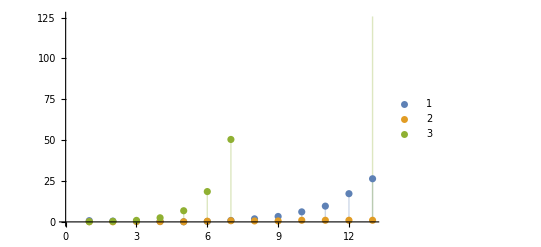

```mathematica
ListPlot[{{0.7576825830783951,0.49644841267890266,0.35687520992649735,0.31163854703628324,0.07145667764492322,0.2697005271981798,0.8684136158685215,1.8755302548962696,3.3227293820725943,6.132727790285841,9.650298234473565,17.262572421367413,26.39498377364014},{0.09385728534846272,0.04793075166504916,0.2659397483555301,0.1611436806243113,0.08378107315221262,0.4202593117053789,0.7157075196016977,0.5886098628960618,0.5776224439909204,1.,1.,1.,1.},{0.125,0.33978522855738064,0.9236320123663312,2.5106921153984585,6.82476875414303,18.551644887822075,50.42859918659189,137.0791448035573,372.61974838021604,1012.8854909469229,2753.3082243508393,7484.267714399727,20344.34892737549}},Filling->Axis,PlotLegends->Automatic]
```

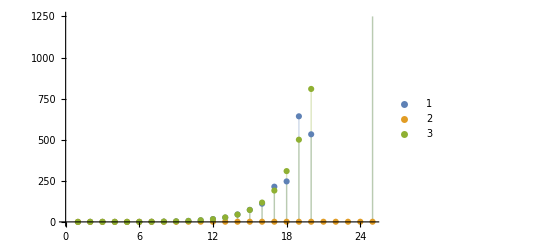

```mathematica
ListPlot[{{0,0.49644841267890266,0.35687520992649735,0.3116385470362833,0.07145667764492322,0.26970052719817983,0.8684136158685214,1.87553025489627,3.3227293820725943,6.132727790285842,9.650298234473565,17.26257242136741,26.39498377364014,45.34592017597571,73.34477209285912,110.84066173804285,214.38000203321468,246.39374770726113,642.5631631327632,533.0793919209951,1736.4606776418887,1736.0636523782646,2732.056264720582,10397.343913398103,8677.11223359115},{0,0.04793075166504916,0.26593974835552997,0.16114368062431117,0.08378107315221262,0.42025931170537906,0.7157075196016978,0.5886098628960621,0.5776224439909204,1.,1.,1.,1.,0.9999999999999999,1.,1.,1.,0.9999999999999999,1.,1.,1.,1.,1.,1.,0.9999999999999999},{0,0.36414848317748766,0.38916882617050125,0.2927980287484293,0.08478293913127026,0.2768095049692339,0.873727565418054,1.84332461988211,3.410300998827484,5.939814960807965,10.024292779047254,16.62463561159246,27.295922556337608,44.5603896852749,72.49673998690578,117.70395149853852,190.83815875618433,309.1271806633799,500.30749109613066,809.1031955009996,1307.241969575178,2111.1995216090186,3405.8361996498816,5489.0287824653415,8841.08237269275}},Filling->Axis,PlotLegends->Automatic]
```

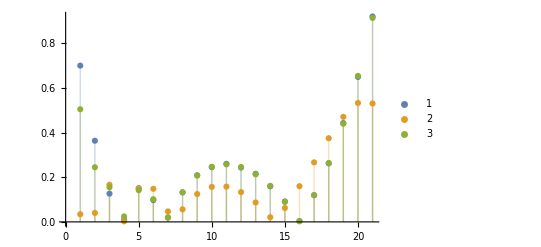

```mathematica
ListPlot[{{0.7003146995730973,0.36376067846877014,0.126479595336767,0.00895962184713644,0.15105373809663125,0.09746085661726375,0.019196629937659446,0.13214552877129443,0.20894956065248377,0.24496590104740248,0.2602053507366578,0.2434732870439051,0.2156072008713046,0.1594866153280291,0.09159359228645307,0.0037555014204229153,0.11960933866967927,0.2623662956686155,0.4429425824668831,0.6495407284896234,0.9205898033293998},{0.03431679538652964,0.04033091973667771,0.16669507897385605,0.0025688717718422073,0.1501157240645613,0.1482377447654981,0.04691848283479592,0.056139978191313535,0.12469693886783939,0.1567645588509229,0.15798245556172227,0.13353226926447356,0.08700272946039095,0.0209171104934611,0.062429262902758284,0.16001732305253544,0.26695790740806014,0.3750180970207055,0.4707100763065177,0.5329468875447226,0.5306106846576928},{0.5048063854846714,0.24482355885523643,0.15542618406391745,0.024691821171533603,0.14191626705422802,0.1017377432362013,0.020376571932003644,0.13267943631395016,0.20749011803100675,0.24693443666629322,0.2579673568341169,0.2458097117880368,0.2133304887996738,0.16152999834506138,0.08999133746270753,0.0028421201934718714,0.11954589366621776,0.26371413707640085,0.44000526362562586,0.6543061003433688,0.9139118482088006}},Filling->Axis,PlotLegends->Automatic]
```

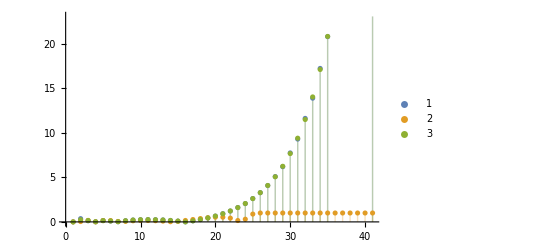

```mathematica
ListPlot[{{0,0.36376067846877014,0.126479595336767,0.008959621847136601,0.15105373809663125,0.09746085661726386,0.019196629937659516,0.13214552877129446,0.20894956065248377,0.24496590104740248,0.2602053507366578,0.24347328704390514,0.21560720087130464,0.15948661532802905,0.09159359228645302,0.0037555014204230467,0.11960933866967927,0.2623662956686156,0.44294258246688306,0.6495407284896234,0.9205898033293999,1.2193947212027823,1.6164262995491272,2.055500139529008,2.624515101345302,3.284107701249999,4.083625833280626,5.092077648518771,6.202550885406406,7.748586269855525,9.30470211102434,11.628892813345576,13.90338793535226,17.24210020113569,20.81517292275064,25.28290937522429,31.29459802171091,36.77744822804405,47.111786289453825,53.489934717226554,70.39584173334448},{0,0.04033091973667771,0.16669507897385605,0.0025688717718419557,0.15011572406456153,0.1482377447654982,0.046918482834795903,0.05613997819131372,0.12469693886783924,0.15676455885092308,0.15798245556172225,0.13353226926447362,0.08700272946039095,0.020917110493461195,0.06242926290275841,0.16001732305253566,0.2669579074080603,0.3750180970207057,0.47071007630651807,0.5329468875447227,0.5306106846576929,0.4213214860670587,0.1553566146860598,0.30269213716998905,0.8789296324483188,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.9999999999999999,1.,1.,1.,1.,1.,1.},{0,0.24482355885523643,0.15542618406391745,0.02469172225268257,0.14191626705422802,0.10173774323620144,0.02037657193200358,0.13267943631395004,0.20749011803100675,0.2469344366662933,0.257967356834117,0.24580971178803684,0.21333048879967392,0.16152999834506135,0.08999133746270745,0.002842120193471987,0.11954589366621776,0.26371413707640107,0.44000526362562586,0.6543061003433686,0.9139118482088008,1.2277962248225602,1.606946034203224,2.0647669287484254,2.617622469347303,3.2853864299509206,4.0923313861493575,5.067872356218042,6.248076968069373,7.676466173351917,9.406128025041523,11.50184671588466,14.042111107682187,17.12283808182918,20.837244917679318,25.3963367692678,30.903650046838344,37.591140766956265,45.71696737876767,55.58779844797523,67.58532421597535}},Filling->Axis,PlotLegends->Automatic]
```

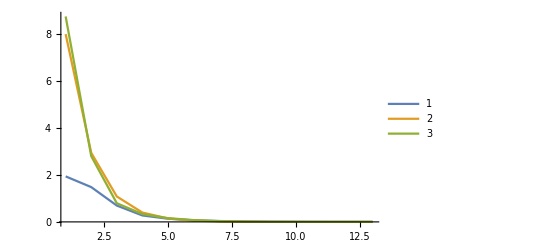

```mathematica
ListLinePlot[{Subscript[A, 2i],Subscript[EX, 2i],Subscript[T, 2i]},PlotLegends->Automatic,PlotRange->All]
```

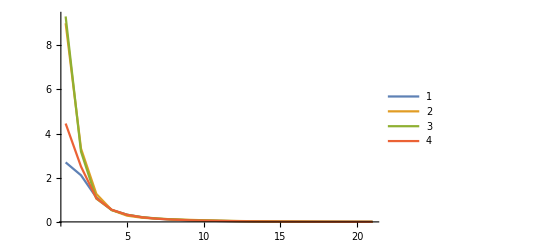

```mathematica
ListLinePlot[{Subscript[A, 10i],Subscript[EX, 10i],Subscript[T, 10i],Subscript[A^o, 3(10)]},PlotLegends->Automatic,PlotRange->All]
```

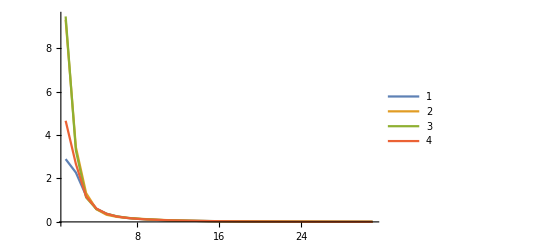

```mathematica
ListLinePlot[{Subscript[A, 28i],Subscript[EX, 28i],Subscript[T, 28i],Subscript[A^o, 3(28)]},PlotLegends->Automatic,PlotRange->All]
```

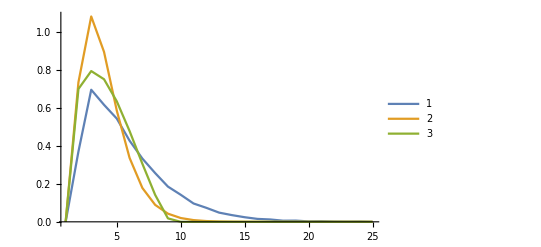

```mathematica
ListLinePlot[{Subscript[Ā, 2i],Subscript[OverTilde[EX], 2i],Subscript[T̄, 2i]},PlotLegends->Automatic,PlotRange->All]
```